We define the direct correlation function for hard spheres within PY approximation.
Wertheim found this expression (PRL 1963) for the direct correlation c(r/d):

```mathematica
c[x_,η_]:=Piecewise[{{-((1+2η)^2-6η(1+η/2)^2 x+η(1+2η)1/2 x^3)/(1-η)^4,x<1}},0]
```

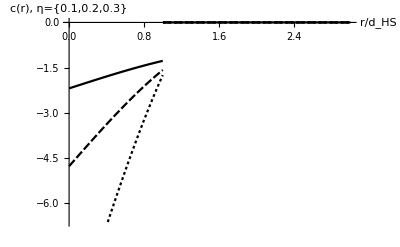

```mathematica
Plot[  {c[x,0.1],c[x,0.2],c[x,0.3]}  ,{x,0,3}    ,PlotTheme->"Monochrome",AxesLabel->{"r/d_HS","c(r), η={0.1,0.2,0.3}"}]
```

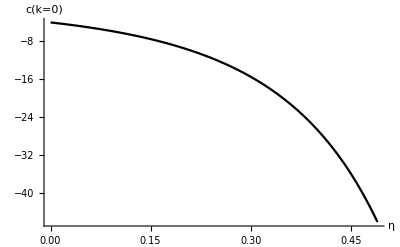

```mathematica
Plot[
Quiet@NIntegrate[   4π r^2 c[r,η]   , {r,0,1} ]
,{η,0,0.49},PlotTheme->"Monochrome",AxesLabel->{"η","c(k=0)"}]
```

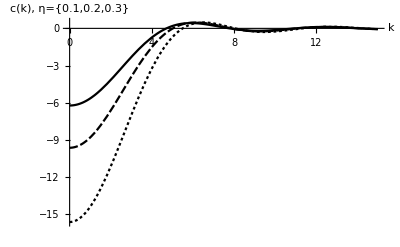

```mathematica
Plot[
{Quiet@NIntegrate[   4π r^2 Sinc[k*r] c[r,0.1]   , {r,0,1} ],
Quiet@NIntegrate[   4π r^2 Sinc[k*r] c[r,0.2]   , {r,0,1} ],
Quiet@NIntegrate[   4π r^2 Sinc[k*r] c[r,0.3]   , {r,0,1} ]}
,{k,0,15},PlotTheme->"Monochrome",AxesLabel->{"k","c(k), η={0.1,0.2,0.3}"}]
```